# Demo

```mathematica
SetDirectory@NotebookDirectory[];
assoc=Get["wickSATdata.txt"];
```

Vertical gray lines indicate where numerical approximation (e.g. TSVD) was used, since A was not invertible

```mathematica
assoc["timeStep"]
```

0.0909091

RANDOMLY CHOOSE INITIAL PARAMS, RECORD PROJ IN GROUND AND FIRST EXCITED STATE, MONITOR CONVERGENCE
SEE RESULTS

FOR 3SAT, use QAOA Ansatz

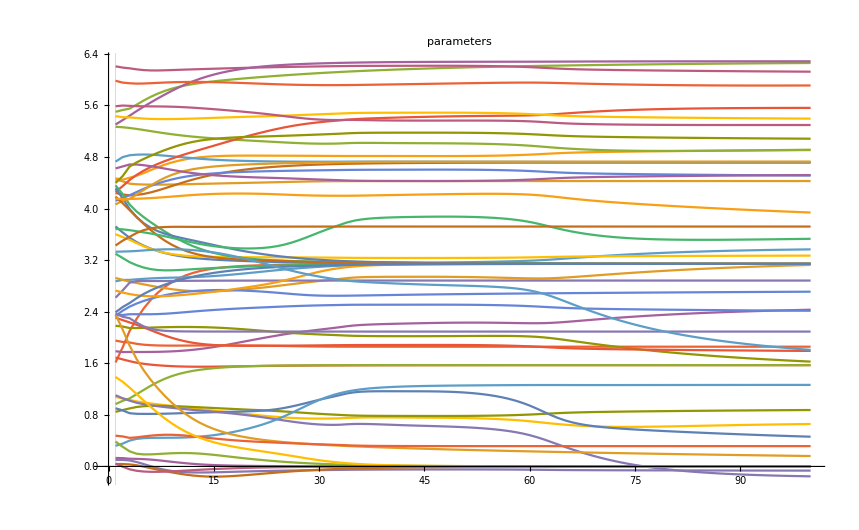

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	%, PlotRange->All, PlotLabel-> "parameters",
	 GridLines -> {assoc["recoveredIterations"], {}}
]
```

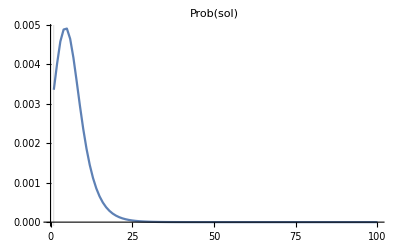

```mathematica
ListLinePlot[
	assoc["solProbEvo"], PlotLabel-> "Prob(sol)",
	GridLines -> {assoc["recoveredIterations"], {}},
	PlotRange->All
]
```

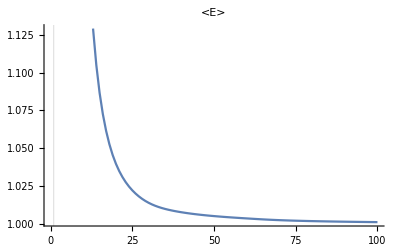

```mathematica
ListLinePlot[
	assoc["expectedEnergyEvo"], PlotLabel -> "<E>",
	GridLines -> {assoc["recoveredIterations"], {}}
]
```

## Behaviour list

- Stuck in energy eigenstate, experiences a point of sharp param jumps without needing TVSD:
 ./Variational3SATSolver 8 24 0 0.9 0 80 0 1 0.1
 This was remedied by Tikhonov regularisation! Wew

# Analysis

```mathematica
discreteColors[n_]:=
	With[
		{partL=Ceiling[Sqrt[n]]},
		DeleteCases[Flatten[Transpose[Partition[Table[Lighter[Darker[Hue[c],.1],.25],{c,0,1-1/n,1/n}],partL,partL,1,0]]],0]
	]
```

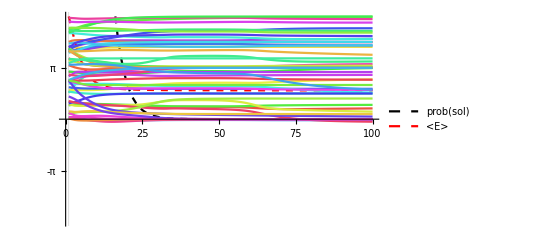

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	Join[
		{assoc["solProbEvo"]/Mean[assoc["solProbEvo"]]},
		{assoc["expectedEnergyEvo"]/Max[assoc["expectedEnergyEvo"]]},
		%/Max@%
	], 
	 GridLines -> {assoc["recoveredIterations"], {}},
	Ticks -> {Automatic,{{-π/Max@%, -π}, {π/Max@%, π}}},
	PlotStyle-> Join[{Directive[Black,Dashed], Directive[Red,Dashed]},discreteColors@Length@%],
	PlotLegends-> Placed[{"prob(sol)", "<E>"},{{.4,.8}}],
	PlotRange->{-1,1}
]
```

```mathematica
s
```

s